```mathematica
Get[URLDownload["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-wind-instruments/Std01-m120.wl"]];
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

C:\Users\mona_\AppData\Local\Temp\Std01-m120-161b75c5-6e58-4907-b239-25b11fa45d17.wl        22.7.2026 21:13:20.    (128794 Bytes)

Clear::wrsym: Symbol Discard is Protected.

SetDelayed::write: Tag Discard in Discard[M_,S_] is Protected.

```mathematica
MyTS = {FontColor->GrayLevel[0],FontFamily->"Lucida Sans Unicode",FontSlant->"Plain",FontWeight->"Plain",FontSize->24};
```

```mathematica
Clear[AP,ToEnglish,Z,newID]

{ToEnglish,Z} = Get[URLDownload["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-wind-instruments/EmissionRatePlotData.dat"]];

newID = {"C2"->"P1","F1"->"P2","F10"->"P3","F11"->"P4","F12"->"P5","F13"->"P6","F14"->"P7","F15"->"P8","F16"->"P9","F17"->"P10","F18"->"P11","F19"->"P12","F2"->"P13","F20"->"P14","F3"->"P15","F4"->"P16","F5"->"P17","F6"->"P18","F7"->"P19","F9"->"P20","O10"->"P21","O11"->"P22","O12"->"P23","O2"->"P24","O3"->"P25","O4"->"P26","O5"->"P27","O6"->"P28","O7"->"P29","O8"->"P30","O9"->"P31","S1"->"P32","S10"->"P33","S11"->"P34","S12"->"P35","S2"->"P36","S3"->"P37","S4"->"P38","S5"->"P39","S6"->"P40","S7"->"P41","S8"->"P42","S9"->"P43","T1"->"P44"};

AP = Union[First/@newID]
Length[AP]
```

{C2,F1,F10,F11,F12,F13,F14,F15,F16,F17,F18,F19,F2,F20,F3,F4,F5,F6,F7,F9,O10,O11,O12,O2,O3,O4,O5,O6,O7,O8,O9,S1,S10,S11,S12,S2,S3,S4,S5,S6,S7,S8,S9,T1}

44

```mathematica
Clear[Z]
Z = Get[URLDownload["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-wind-instruments/EmissionRates.dat"]];
Length[Z]
```

1804

```mathematica
Clear[pl,W,Y]
Y = {"Proband","Instrument","Player","Task","Bins","EmissionRateSignificanceLevel","EmissionRateµσCI","EmissionRateDistribution"}/.Z;
Y = Select[Y,UnsameQ[#[[8]],"EmissionRateDistribution"]&];
Y = Select[Y,(#[[7,4]]>=0.01)&];
Y = Select[Y,(#[[6]]>=0.001)&];
Y = Map[ReplacePart[#,DeleteDuplicates[Last/@#[[5]]],5]&,Y];
Y = Select[Y,(Length[#[[5]]]==1)&];
Y = Transpose[Y];
Y[[5]] = First/@Y[[5]];
Y[[5]] = Y[[5]]/."Aerosol"->N[-1];
Y[[1]] = Y[[1]]/.ToEnglish;
Y[[4]] = Y[[4]]/.ToEnglish;
Y[[7]] = LessEqual@@@Map[Insert[Clip[Drop[#,2],{0,Infinity}],x,2]&,Y[[7]]];
Y[[7]] = Function/@(Y[[7]]/.x->#);
Y = Join[Take[Y,5],Y[[{8,7}]]];
Y = Transpose[Y];
Y = Select[Y,MemberQ[AP,#[[1]]]&];
Y = Select[Y,UnsameQ[#[[5]],"Droplets"]&];
Y = Select[Y,(#[[5]]<=5)&];                                              (*    Aerosol    *)
Union[Map[#[[5]]&,Y]]
Length[Y]
```

{-1.,0.251496,0.40694,0.8,1.57226,2.99099}

868

```mathematica
W = pl = {,,};
```

```mathematica
Clear[b,f,fs0,fs1,fs2,G,H,h,l,M,P,p,Q,q,R,S,s,T,t,v,X]
t = {"Breathing","Playing","Playing With Surgical Mask","Speaking","Speaking With Surgical Mask"}[[

5 (*hier manuell durch die Aufgabennummern durchgehen um die Abb. zu erzeugen. Kann mit Filter KG angewendet werden und ohne*)

]]
```

Speaking With Surgical Mask

```mathematica
X = Select[Y,(#[[4]]===t)&];
X = MyPartition[1,X];
X = Select[X,(Length[#[[2]]]==6)&];
X = Map[{Prepend[Take[#[[2,1]],2],#[[1]]],SortBy[Map[Drop[#,3]&,#[[2]]],First]}&,X];
X = Map[(
h = #[[2,1,2]];
h = PDF[h,x];
h[[1,1,1]] /= NIntegrate[h,Apply[List,#[[2,1,3]][x]][[{2,1,3}]]];
h = ReplacePart[h,#[[2,1,3]][x],{1,1,2}];
ReplacePart[#,Function[x,Evaluate[h]],{2,1}]
)&,X];
Max[Abs[Map[NIntegrate[#[[2,1,2]],{x,0,Infinity}]&,X]-1]]

X = Map[{Append[#[[1]],#[[2,1]]],Rest[#[[2]]]}&,X];
X = Transpose[X];
X[[2]] = Transpose/@Map[{#[[1]],Select[RandomVariate[#[[2]],

500000

],#[[3]]]}&,X[[2]],{2}];
X[[2]] = Transpose[X[[2]]];
b = X[[2,1]];
b = DeleteDuplicates[b];
If[Length[b]==1,
b = First[b]]

X[[2]] = X[[2,2]];
h = Min[Map[Length,X[[2]],{2}]]

X[[2]] = Transpose/@Map[Take[#,h]&,X[[2]],{2}];
X[[2]] = Map[{h=Total[#],#/h}&,X[[2]],{2}];
X = Transpose[X];
X = Transpose[
Map[(
h = #[[1,4]];
{Most[First[#]],
Map[{Round[100*#[[2]]],{h[#[[1]]]}}&,#[[2]]]}
)&,X]];
X[[2]] = Transpose/@Map[(Join@@Outer@@Prepend[#,List])&,X[[2]],{2}];
X[[2]] = Map[
Map[
ReplacePart[#,Total[Flatten[#[[2]]]],2]&,
MyPartition[1,#]]&,
X[[2]],{2}];
X[[2]] = Map[
Transpose[Select[#,(#[[2]]>0)&]]&,
X[[2]],{2}];
X = Transpose[X];
X = Select[X,Not[MemberQ[#[[2]],{}]]&];
Length[X]

X = Transpose[X];
X[[2]] = Map[ReplacePart[#,#[[2]]/Total[#[[2]]],2]&,X[[2]],{2}];
X[[2]] = Map[Transpose[Append[#,Rest[FoldList[Plus,0,#[[2]]]]]]&,X[[2]],{2}];
X[[2]] = Map[{Select[#,(0.05<#[[3]]<=0.95)&],#}&,X[[2]],{2}];
X[[2]] = Map[If[Length[#[[1]]]>2,#[[1]],#[[2]]]&,X[[2]],{2}];
X[[2]] = Map[Most[Transpose[#]]&,X[[2]],{2}];
X[[2]] = Map[(Join@@ConstantArray@@@Transpose[ReplacePart[#,Round[10000*#[[2]]/Total[#[[2]]]],2]])&,X[[2]],{2}];
X = Transpose[X];
```

2.22045×10^-16

{0.251496,0.40694,0.8,1.57226,2.99099}

20569

16

```mathematica
p = First/@First/@X;
p = p/.newID;
p = SortBy[p,ToExpression[StringDrop[#,1]]&];
i = 8;
i *= Range[0,Quotient[Length[p],i]];
If[Last[i]!=Length[p],
AppendTo[i,Length[p]]];
i = Transpose[{Most[i]+1,Rest[i]}];
p = Map[ConcatStringList[Take[p,#]," "]&,i];
p = ConcatStringList[p,"\n"]
p = {p};
q = {ToLowerCase[t]};
r = t/.{"Breathing"->1,"Speaking"->2,"Speaking With Surgical Mask"->3};
h = {{0.2,0.5,0.8}[[r]]};
```

P2 P3 P8 P11 P14 P15 P19 P20
P25 P26 P32 P33 P35 P37 P40 P41

```mathematica
X = {X};
X = Map[Last,X,{2}];
X = Map[(Join@@@Transpose[#])&,X];
X = Map[Join[#,Flatten[Outer[ConstantArray,MinMax[#],{Round[0.05*Length[#]]}]]]&,X,{2}];
  W[[r]] = X;
pl[[r]] = {
GrayLevel[0],Map[
Text[
Style[#[[1]],FontSize->fs1,FontWeight->"Plain"],
Scaled[{#[[2]],v=0.985}],{0,1}]&,
Transpose[{q,h}]],
GrayLevel[0.5],Map[
Text[
Style[#[[1]],FontSize->fs2,FontWeight->"Plain"],
Scaled[{#[[2]],v-0.05}],{0,1}]&,
Transpose[{p,h}]]};
```

```mathematica
fs0 = 18;
fs1 = 24;
fs2 = 14;
```

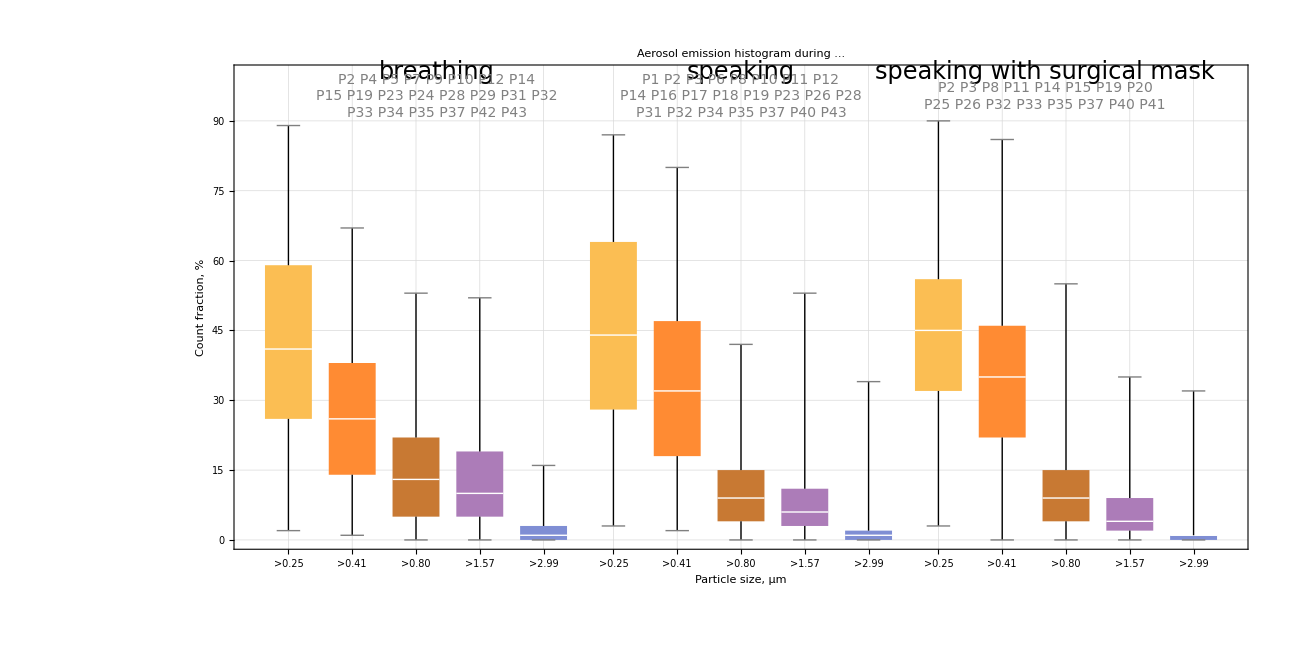

```mathematica
G = BoxWhiskerChart[Join@@W,
{{"Whiskers",Thick}},
AspectRatio->0.5,
Axes->False,
ChartLabels->Map[Style[StringJoin[">",RealForm[#,4,2]],fs0]&,b],
DisplayFunction->Identity,
Frame->True,
FrameLabel->(f={"Particle size,  µm","Count  fraction,  %"}),
GridLines  ->Automatic,
ImageSize->1300,
LabelStyle->MyTS,
PlotLabel->(l="Aerosol emission histogram during ..."),
PlotRange->{All,{0,100}},
Prolog->pl]
```

```mathematica
Export[NotebookDirectory[]~~"output directory\\"~~"Aerosol emission histograms.svg",G]
```

E:\Stier\Projects\Firle\Auswertung Sprechen-Atmen-MNS\Aerosol emission histograms.svg

```mathematica
Clear[GG]
```

```mathematica
GG = G;
```

```mathematica
GG = Insert[GG,FontFamily->"Lucida Sans Unicode",ReplacePart[Position[GG,"breathing"                                         ][[1]],2,-1]];
GG = Insert[GG,FontFamily->"Lucida Sans Unicode",ReplacePart[Position[GG,"speaking"                                           ][[1]],2,-1]];
GG = Insert[GG,FontFamily->"Lucida Sans Unicode",ReplacePart[Position[GG,"speaking with surgical mask"][[1]],2,-1]];
```

```mathematica
GG = ReplacePart[GG,None,{Position[G,FrameTicks][[1,1]],2,2,2}];
GG = Fold[
Insert[#1,#2,2]&,GG,
{PlotRangePadding->{{Scaled[0.025],Scaled[0.025]},{Scaled[0.025],None}},
GridLines->{{5.55,10.65},None},
GridLinesStyle->{{AbsoluteThickness[1],GrayLevel[0]},Automatic},
Nothing
}];
```

```mathematica
GG = GG/.{
0.935->0.92,
0.985->0.99};
```

```mathematica
Prolog/.Rest[List@@GG]
```

{{GrayLevel[0],{Inset[breathing,Scaled[{0.2,0.99}],ImageScaled[{1/2,1}]]},GrayLevel[0.5],{Inset[P2 P4 P5 P7 P9 P10 P12 P14
P15 P19 P23 P24 P28 P29 P31 P32
P33 P34 P35 P37 P42 P43,Scaled[{0.2,0.92}],ImageScaled[{1/2,1}]]}},{GrayLevel[0],{Inset[speaking,Scaled[{0.5,0.99}],ImageScaled[{1/2,1}]]},GrayLevel[0.5],{Inset[P1 P2 P3 P6 P8 P10 P11 P12
P14 P16 P17 P18 P19 P23 P26 P28
P31 P32 P34 P35 P37 P40 P43,Scaled[{0.5,0.92}],ImageScaled[{1/2,1}]]}},{GrayLevel[0],{Inset[speaking with surgical mask,Scaled[{0.8,0.99}],ImageScaled[{1/2,1}]]},GrayLevel[0.5],{Inset[P2 P3 P8 P11 P14 P15 P19 P20
P25 P26 P32 P33 P35 P37 P40 P41,Scaled[{0.8,0.92}],ImageScaled[{1/2,1}]]}}}

{{20,2,3,2,1,2}}

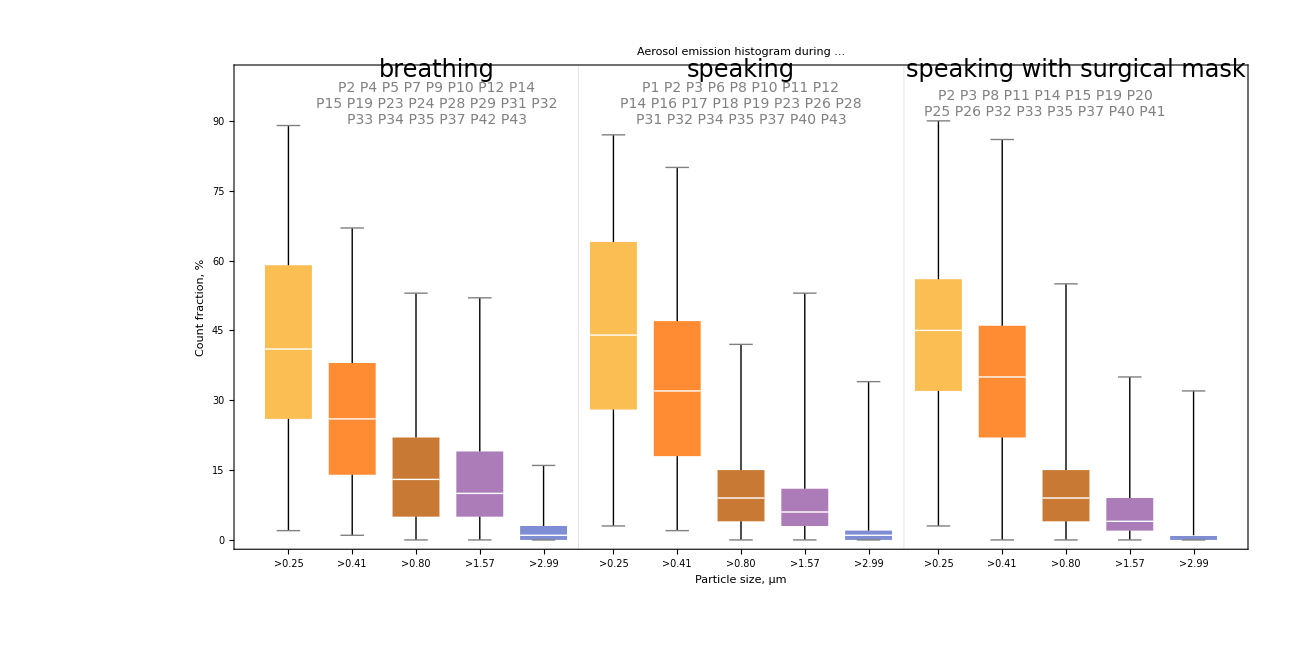

```mathematica
Position[       GG,Scaled[{0.8,0.99}]]
ReplacePart[GG,Scaled[{0.83,0.99}],%[[1]]]
```

```mathematica
Position[         %,Scaled[{0.8,0.92}]]
ReplacePart[%%,Scaled[{0.87,0.92}],%[[1]]]
```

{{20,2,3,4,1,2}}

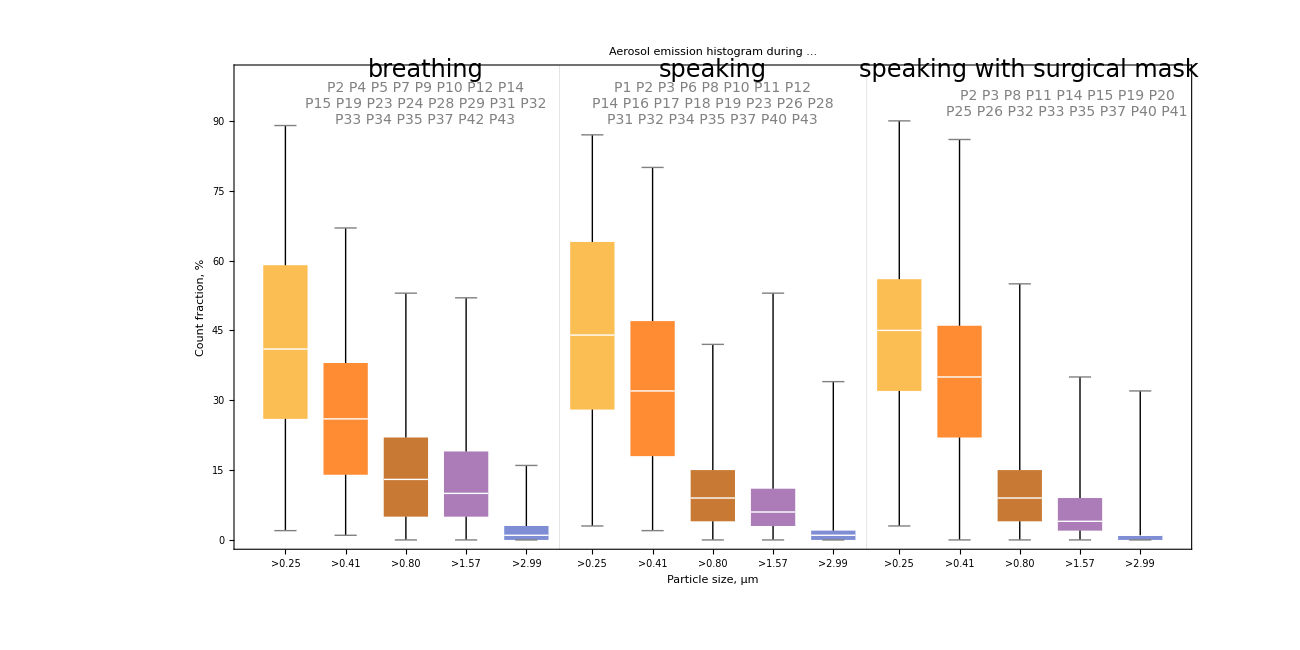
```mathematica
-Graphics-;
```

```mathematica
Export[NotebookDirectory[]~~"output directory\\"~~"Aerosol emission histograms 2.svg",%]
```

E:\Stier\Projects\Firle\Auswertung Sprechen-Atmen-MNS\Aerosol emission histograms 2.svg

```mathematica
(*    ENDE    *)
```